Math 124 - Programming for Mathematical Applications
UC Berkeley, Spring 2021

Homework 12
Due Friday April 28

Problem 1
It is well known that ∑_(i=1)^n i=1/2 n (1+n). Make a table with similar formulas for  ∑_(i=1)^n i^k, with k ranging from 1 to 8.

```mathematica
P1Answer = Table[Sum[i^k, {i, 0, n}], {k, 1, 8}]
```

{1/2 n (1+n),1/6 n (1+n) (1+2 n),1/4 n^2 (1+n)^2,1/30 n (1+n) (1+2 n) (-1+3 n+3 n^2),1/12 n^2 (1+n)^2 (-1+2 n+2 n^2),1/42 n (1+n) (1+2 n) (1-3 n+6 n^3+3 n^4),1/24 n^2 (1+n)^2 (2-4 n-n^2+6 n^3+3 n^4),1/90 n (1+n) (1+2 n) (-3+9 n-n^2-15 n^3+5 n^4+15 n^5+5 n^6)}

Problem 2
Use the Factor function to prove that the product of four consecutive numbers plus one is always a squared number.

```mathematica
P2Answer=Factor[(x)*(x+1)*(x+2)*(x+3)+1]
```

(1+3 x+x^2)^2

Problem 3
Show that the formula n^2+n+41 produces prime numbers for n from 0 to 39.

```mathematica
P3=Table[n^2+n+41,{n,0,39}]
P3Answer=Table[PrimeQ[j],{j,P3}]
```

{41,43,47,53,61,71,83,97,113,131,151,173,197,223,251,281,313,347,383,421,461,503,547,593,641,691,743,797,853,911,971,1033,1097,1163,1231,1301,1373,1447,1523,1601}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Problem 4
11 is the first prime number with all digits equal to 1. Find the next one (using a loop).

```mathematica
n=111;While[PrimeQ[n]≠True,n=(n*10+1)];Print[n]
```

1111111111111111111

Problem 5
Define the function f(x) as follows:

	f(xy)=f(x)+f(y)
f(x^n)=nf(x)
f(n)=0

where n is an integer. Show that

	f(∏_(k=1)^20 k!(x_k)^k)=∑_(k=1)^20 k f(x_k)

```mathematica
Clear[f]
Clear[n]
f[x_*y_]:=f[x]+f[y];
f[x_^n_Integer]:=n*f[x];
f[n_Integer]:=0;
```

```mathematica
Print[f[Product[(i!)*(x[i]^i), {i, 0, 20}]]]
Print[Sum[i*f[x[i]], {i, 0, 20}]]
f[Product[(i!)*(x[i]^i), {i, 0, 20}]] == Sum[i*f[x[i]], {i, 0, 20}]
```

f[x[1]]+2 f[x[2]]+3 f[x[3]]+4 f[x[4]]+5 f[x[5]]+6 f[x[6]]+7 f[x[7]]+8 f[x[8]]+9 f[x[9]]+10 f[x[10]]+11 f[x[11]]+12 f[x[12]]+13 f[x[13]]+14 f[x[14]]+15 f[x[15]]+16 f[x[16]]+17 f[x[17]]+18 f[x[18]]+19 f[x[19]]+20 f[x[20]]

f[x[1]]+2 f[x[2]]+3 f[x[3]]+4 f[x[4]]+5 f[x[5]]+6 f[x[6]]+7 f[x[7]]+8 f[x[8]]+9 f[x[9]]+10 f[x[10]]+11 f[x[11]]+12 f[x[12]]+13 f[x[13]]+14 f[x[14]]+15 f[x[15]]+16 f[x[16]]+17 f[x[17]]+18 f[x[18]]+19 f[x[19]]+20 f[x[20]]

True

Problem 6
a) Plot the function f(x)=e^-x/(2+sin(x^2)) and its tangent line g(x) at x=1 for x∈[0,3].
b) Calculate the integral of f(x)-g(x) between x=0 and x=1 numerically with 100 digits.

```mathematica
f1[x_]=Exp[-x]/(2+Sin[x^2])
```

ⅇ^-x/(2+Sin[x^2])

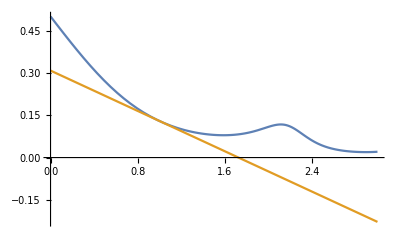

```mathematica
Plot[{f1[x], f1'[1] (x - 1) + f1[1]}, {x, 0, 3}]
```

```mathematica
NIntegrate[(f1[x] - (D[f1[x],x])),{x, 0, 1},WorkingPrecision->100]
```

0.6560225894307646832353054882557920612015043021329287922640223352970395793762171706166899933516202368

Problem 7
Define the following piecewise function:
	f(x)=Piecewise[{{-x, if |x|<1}, {sin(x), if 1≤|x|<2}, {cos(x), otherwise.}}]
a) Plot f(x) between x=-3 and x=3.
b) Calculate the integral of 1/(1+(f(x))^2) between x=-3 and x=3 (symbolically).

```mathematica
f2[x_]=Piecewise[{{-x,Abs[x]<1},{Sin[x],1≤Abs[x]<2},{Cos[x],Abs[x]≥2}}]
```

Piecewise[{{-x, Abs[x]<1}, {Sin[x], 1≤Abs[x]<2}, {Cos[x], Abs[x]≥2}, {0, True}}]

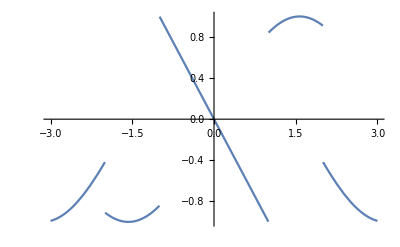

```mathematica
Plot[f2[x],{x,-3,3}]
```

```mathematica
Integrate[1/(1+f2[x]^2),{x,-3,3}]
```

1/2 (π+2 √2 ArcCot[((2-Cos[2]+Cos[4]) Cot[1])/(√2)]+2 √2 ArcCot[(Cot[1]+Sin[2])/(√2)])